# Lista 05 - Introdução à Física Computacional I

Lyliana Myllena Santos de Sousa - 11223740
Lyliana.sousa@usp.br

Ao preparar o Notebook da lista, faça uso abundante de comentários e textos explicativos. Não se esqueça de rotular devidamente os eixos dos gráficos que produzir.

No mesmo espírito do mapa logístico, estude o mapa do seno, definido por: x_(n + 1) = a Sin[π x_n]

## 1.

Escolhendo a = 0.75, faça um gráfico contendo, no mesmo conjunto de eixos, a função identidade, y = x,  a função que define o mapa do seno, y = f(x) ≡ a Sin[π x_n] e a função y  = f (f(x)), todas no intervalo 0 ≤ x ≤ 1. Com base nesse gráfico, reflita se, para esse valor de a, o atrator do mapa do seno corresponde a um ponto fixo x = 0, a um ponto fixo x = x^*≠ 0 ou a um ciclo 2.

```mathematica
f[a_][x_]:=a*Sin[π x];
optam={ImageSize->Large,LabelStyle-> {"Large"}};
```

```mathematica
grafmapa[a_,x0_,n_]:=
(
xx=x0;
lista1={{xx,0},{xx,f[a][xx]}};
Do[
(
xx=f[a][xx];AppendTo[lista1,{xx,xx}];
AppendTo[lista1,{xx,f[a][xx]}]),
{i,1,n}
];
grafico0=Plot[{x,f[a][x],Nest[f[a],x,2]},{x,0,4},Evaluate[optam],AxesLabel->{"x","f(x)"}];
Show[{grafico0,ListLinePlot[lista1,PlotStyle->Red]}]
)
```

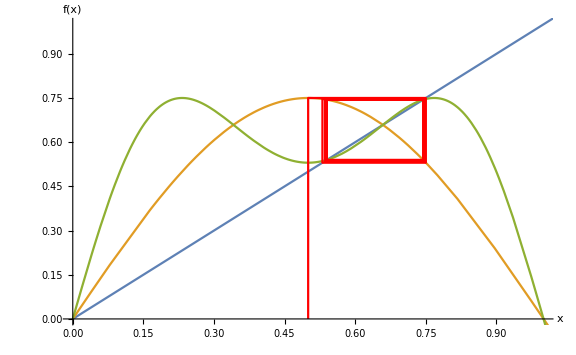

```mathematica
Show[grafmapa[0.75,0.5,10],PlotRange->{{0,1},{0,1}}]
```

(Resposta) Analisando o gráfico observamos que há uma alternância entre dos valores de x, sendo eles {0.540177, 0.744034}, com isso dizemos que há um ciclo 2.

## 2.

Produza um diagrama de bifurcações do mapa do seno utilizando 1000 valores de a entre 0 e 1. Para cada valor de a, certifique-se de haver descartado um número suficiente de aplicações do mapa para que o atrator esteja refletido fidedignamente no diagrama de bifurcações. Com base no diagrama, verifique se suas conclusões do item anterior estavam corretas. Se estiver usando o Mathematica, é melhor fazer uso de Compile quando definir a função, para garantir que o tempo de execução não seja muito longo.

```mathematica
pontos:=Compile[{a,{m,_Integer},{n,_Integer}},
(
xlista=Drop[NestList[a*Sin[π #]&,0.5,n],m+1];
saida={};
Do[AppendTo[saida,{a,xlista[[i]]}],{i,1,Length[xlista]}];
saida
),{{saida,_Real,2}}]
```

```mathematica
varrepontos:=Compile[{amin,amax,na,{m,_Integer},{n,_Integer}},
(
grandelista={};
Do[AppendTo[grandelista,pontos[a,m,n]],{a,amin,amax,(amax-amin)/na}];
Flatten[grandelista,1]
),{{grandelista,_Real,3}}]
```

```mathematica
diagbifurca[amin_,amax_,na_,m_,n_]:=ListPlot[varrepontos[amin,amax,na,m,n],Axes->False,Frame->True,FrameLabel->{"a","x"},PlotStyle->PointSize[0.001],AspectRatio->1,Evaluate[optam]]
```

```mathematica
diagbifurca[0,1,1000,1024,2048]
```

-Graphics-

## 3.

Determine, com precisão de máquina, os menores valores de a entre 0 e 1 que tornam instáveis os ciclos com período n entre 2 e 128.  Pode ser útil traçar ampliações dos diagramas de bifurcação de modo a encontrar palpites adequados para os valores de a.

A primeira bifurcação acontece nos pontos {0.7148451021114569, 0.6456078632836839}, obtidos pelo cursor do Mathematica. Assim, faremos o diagrama de bifurcação indo de 0.70 à 1.

```mathematica
Show[diagbifurca[0.70,1,1000,1024,2048]]
```

-Graphics-

A seguir teremos uma lista com os três pontos principais da bifurcação obtidos pelo cursor do Mathematica.

```mathematica
l1 = {{0.7183363244204428,0.6462489626960639},{0.8316606570512821,0.823911907767147},{0.8316606570512821,0.4485989363044842}};
```

Agora faremos uma novo diagrama de bifurcação indo observando a “terceira região” de bifurcação, onde teremos oito ramificações e estão localizadas na região de a ∈ { 0.86, 0.87}, onde nos concentraremos na região da primeira ramificação de baixo para cima.

```mathematica
Show[diagbifurca[0.863,0.867,1000,1024,2048], PlotRange -> {0.35,0.365} ]
```

-Graphics-

A seguir teremos uma segunda lista com os três pontos principais da segunda bifurcação obtidos pelo cursor do Mathematica.

```mathematica
l2= {{0.864040860826697,0.35870343865829935},{0.8652300910125141,0.3597104480898381},{0.865230091011251,0.35553855187425365} };
```

Agora faremos o mesmo processo, gerando uma terceira lista.

```mathematica
Show[diagbifurca[0.865,0.8658,1000,1024,2048], PlotRange -> {0.3545,0.355} ]
```

-Graphics-

```mathematica
Show[diagbifurca[0.8654,0.8657,1000,1024,2048], PlotRange -> {0.3545,0.355} ]
```

-Graphics-

```mathematica
l3 = {{0.8655628177967821,0.35490377255328953},{0.8655042372882479,0.35493439037716124}};
```

```mathematica
a0 = FindRoot[{x == Nest[f[a],x,1], D[Nest[f[a],x,1],x]== -1}, {{x, l1[[1,2]]},{a,l1[[1,1]]}}]
a1 = FindRoot[{x == Nest[f[a],x,2], D[Nest[f[a],x,2],x]== -1}, {{x, l1[[3,2]]},{a,l1[[3,1]]}}]
a2 = FindRoot[{x == Nest[f[a],x,4], D[Nest[f[a],x,4],x]== -1}, {{x, l1[[2,2]]},{a,l1[[2,1]]}}]
a3 = FindRoot[{x == Nest[f[a],x,8], D[Nest[f[a],x,8],x]== -1}, {{x, l2[[1,2]]},{a,l2[[1,1]]}}]
a4 = FindRoot[{x == Nest[f[a],x,16], D[Nest[f[a],x,16],x]== -1}, {{x, l2[[2,2]]},{a,l2[[2,1]]}}]
a5 = FindRoot[{x == Nest[f[a],x,32], D[Nest[f[a],x,32],x]== -1}, {{x, l2[[3,2]]},{a,l2[[3,1]]}}]
a6 = FindRoot[{x == Nest[f[a],x,64], D[Nest[f[a],x,64],x]== -1}, {{x, l3[[1,2]]},{a,l3[[1,1]]}}]
a7 = FindRoot[{x == Nest[f[a],x,128], D[Nest[f[a],x,128],x]== -1}, {{x, l3[[2,2]]},{a,l3[[2,1]]}}]
```

{x→0.645774,a→0.719962}

{x→0.444794,a→0.833266}

{x→-0.856595,a→0.858609}

{x→0.358643,a→0.864084}

{x→0.359673,a→0.865259}

{x→0.354924,a→0.865511}

{x→0.354901,a→0.865565}

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{x→0.354919,a→0.865466}

## 4.

A partir de uma tabela construída com os resultados do item anterior, obtenha estimativas para a constante δ de Feigenbaum utilizando as bifurcações que marcam a instabilidade dos ciclos de período 2^(j - 1), 2^j e 2^(j + 1). Se a_(j - 1), a_j e a_(j + 1) são os valores de a nessas bifurcações, a estimativa correspondente para a constante de Feigenbaum é δ_j = (a_j - a_(j - 1))(a_(j + 1) - a_j). Suas estimativas sucessivas parecem tender ao valor exato (com 10 algarismos significativos) para o mapa logístico, δ_log = 4.669201609?

```mathematica
δ1 = (0.8332663537456854 - 0.7199616829795352)/(0.8586090599021114 -0.8332663537456854)
```

4.4709

```mathematica
δ2 = (0.8586090599021114 - 0.8332663537456854)/(0.8640841737087172 -0.8586090599021114)
```

4.62871

```mathematica
δ3 = (0.8640841737087172 - 0.8586090599021114)/(0.8652589606966343 -0.8640841737087172)
```

4.66052

```mathematica
δ4 = (0.8652589606966343- 0.8640841737087172)/(0.8655106638228592 -0.8652589606966343)
```

4.66735

```mathematica
δ5 = (0.8655106638228592 - 0.8652589606966343)/(0.865564575509335 -0.8655106638228592)
```

4.6688

## 5.

Seja Δ_j a diferença entre δ_log e suas estimativas δ_j, com j entre 3 e 7. Procure um ajuste para Δ_j da forma C_1 Exp[- C_2j]  e trace os dados e o ajuste no mesmo conjunto de eixos, com as abscissas em escala linear e as ordenadas em escala logarítmica. O que o gráfico sugere a respeito do comportamento de δ_j quando j ≫ 1?

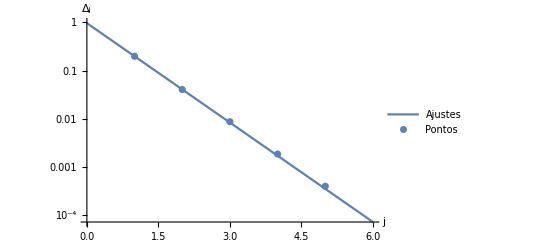

```mathematica
δ = {δ1,δ2,δ3,δ4,δ5};
Δj= 4.669201609 - δ;
jr = {1,2,3,4,5};
dados = Transpose[{jr,Δj}];
ajusteDj[j_]:=C1*Exp[-C2*j]

ajuste =  FindFit[dados, ajusteDj[j], {{C1,0.2},{ C2,1.2}}, j ];
graf1 = LogPlot[ajusteDj[j]/.ajuste,{j,0,6}, PlotLegends->{"Ajustes"}];
graf2 = ListLogPlot[dados, PlotLegends->{"Pontos"}];
Show[{graf1, graf2},AxesLabel-> {"j", "Δ_j"}]
```

O gráfico acima sugere que conforme j tente a infinito Δ_j converge a zero.

## 6.

Finalmente, determine com 3 algarismos significativos o valor do expoente de Lyapunov para o mapa do seno quando a = 1 e faça um gráfico desse expoente para a entre 0.5 e 1. Quais são as regiões em que o mapa exibe comportamento caótico?

```mathematica
lyapunov[a_,x0_,n_,m_]:=
(xlista=Drop[NestList[f[a],x0,n],m+1];
Total[Log[Abs[f[a]'[xlista]]]]/Length[xlista]
)
```

```mathematica
NumberForm[lyapunov[1,0.5,2048,1024] ,3]
```

0.69

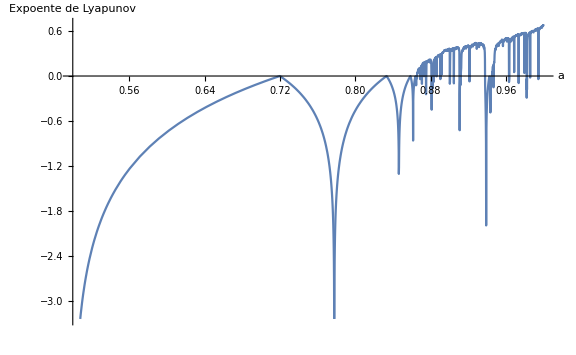

```mathematica
Plot[lyapunov[a,0.5,10000,1000],{a,0.5,1},Evaluate[optam],AxesLabel-> {"a","Expoente de Lyapunov"}]
```

O mapa começara a apresentar comportamento caótico para a ≥ 0.85.